# Subregion Complexity/ Volume Proposal in Empty AdS3 (Vacuum State in CFT2)

## Restart the Kernel

```mathematica
Quit[]
```

## Surfaces in 3D Anti-de Sitter Space

Poincaré Patch coordinates (z,t,x)

```mathematica
(*z=L^2/r*)
```

```mathematica
$Assumptions=And[$Assumptions&&z ∈Reals&&t∈Reals&&x∈Reals&&L∈Reals&&z>0];
$Assumptions=And[$Assumptions&&GN∈Reals&&GN>0];
```

```mathematica
coord={z,t,x};
metric=L^2/z^2{{1,0,0},{0,-1,0},{0,0,1}};
metricsign=-1;
Import["/Users/HugoCamargo89/Documents/Wolfram Mathematica/Mathematica Packages/diffgeo.m"]
```

```mathematica
metric//MatrixForm
```

(L^2/z^2 | 0 | 0
0 | -L^2/z^2 | 0
0 | 0 | L^2/z^2)

```mathematica
Sum[metric[[i,j]] dd[coord[[i]]] dd[coord[[j]]],{i,3},{j,3}]
```

-(L^2 𝕕[t]^2)/z^2+(L^2 𝕕[x]^2)/z^2+(L^2 𝕕[z]^2)/z^2

```mathematica
(*AdS3[z_,t_,x_]:=L^2/z^2(Dt[z]^2-Dt[t]^2+Dt[x]^2);*)
```

```mathematica
(*{Λ->-1/L^2}*)
```

```mathematica
Table[Einstein[[i,j]]-1/L^2 metric[[i,j]]//Simplify,{i,3},{j,3}]
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Table[RicciTensor[[i,j]]+2/L^2 metric[[i,j]]//Simplify,{i,3},{j,3}]
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
RicciScalar//FullSimplify
```

-6/L^2

```mathematica
AdS3[z_,t_,x_]:=L^2/z^2(Dt[z]^2-Dt[t]^2+Dt[x]^2);
```

```mathematica
volumeForm
```

(Abs[L]^3 𝕕[z,t,x])/z^3

```mathematica
rg
```

Abs[L]^3/z^3

```mathematica
Assuming[{ϵ>0,ϵ<zh},Integrate[Integrate[Integrate[rg,{z,ϵ,zh}],{x,x1,x2}],{t,t1,t2}]]
```

1/2 (-t1+t2) (-x1+x2) (-1/zh^2+1/ϵ^2) Abs[L]^3

```mathematica
Assuming[{ϵ>0,ϵ<zh},Integrate[rg,{z,ϵ,zh}]]//FullSimplify
```

1/2 (-1/zh^2+1/ϵ^2) Abs[L]^3

```mathematica
(RicciScalar-2(-1/L^2))//Simplify
```

-4/L^2

```mathematica
Simplify[1/(16 π GN)(rg)*(RicciScalar-2(-1/L^2))]
```

-Abs[L]^3/(4 GN L^2 π z^3)

```mathematica
Assuming[{ϵ>0,ϵ<zh},Integrate[Integrate[Integrate[-1/(16 π GN)(rg)*(RicciScalar-2(-1/L^2)),{z,ϵ,zh}],{x,x1,x2}],{t,t1,t2}]]//FullSimplify
```

((-t1+t2) (-x1+x2) (-1/zh^2+1/ϵ^2) Abs[L])/(8 GN π)

## Geodesic Equations

```mathematica
display[Christoffel]
```

{z,z,z}
{z,t,t}
{t,z,t}
{t,t,z}
{x,z,x}
{x,x,z} | -1/z
{z,x,x} | 1/z

```mathematica
display[(Christoffel/.{z-> z[λ],t-> t[λ],x-> x[λ]})]
```

{z,z,z}
{z,t,t}
{t,z,t}
{t,t,z}
{x,z,x}
{x,x,z} | -1/z[λ]
{z,x,x} | 1/z[λ]

```mathematica
Table[Sum[Christoffel⟦i,j,k⟧D[coord⟦j⟧[λ],λ]D[coord⟦k⟧[λ],λ],{j,1,3},{k,1,3}],{i,1,3}]
```

{-t'[λ]^2/z+x'[λ]^2/z-z'[λ]^2/z,-(2 t'[λ] z'[λ])/z,-(2 x'[λ] z'[λ])/z}

```mathematica
Table[D[coord⟦i⟧[λ],{λ,2}]+Sum[Christoffel⟦i,j,k⟧D[coord⟦j⟧[λ],λ]D[coord⟦k⟧[λ],λ],{j,1,3},{k,1,3}],{i,1,3}]
```

{-t'[λ]^2/z+x'[λ]^2/z-z'[λ]^2/z+z''[λ],-(2 t'[λ] z'[λ])/z+t''[λ],-(2 x'[λ] z'[λ])/z+x''[λ]}

```mathematica
Eq1:=-D[t[λ],λ]^2/z[λ]+D[x[λ],λ]^2/z[λ]-D[z[λ],λ]^2/z[λ]+D[z[λ],{λ,2}];
Eq2:=-(2 D[t[λ],λ] D[z[λ],λ])/z[λ]+D[t[λ],{λ,2}];
Eq3:=-(2 D[x[λ],λ]D[z[λ],λ])/z[λ]+D[x[λ],{λ,2}];
```

```mathematica
Flatten[DSolve[Eq3==0,z[λ],λ]]
```

{z[λ]→C[1] √x'[λ]}

```mathematica
Eq2/.{z[λ]->C[1] √x'[λ],z'[λ]->D[(C[1] √x'[λ]),λ],z''[λ]->D[(C[1] √x'[λ]),{λ,2}]}//FullSimplify
```

t''[λ]-(t'[λ] x''[λ])/x'[λ]

```mathematica
Flatten[DSolve[(t''[λ]-(t'[λ] x''[λ])/x'[λ]==0),t[λ],λ]]//FullSimplify
```

{t[λ]→C[2]+C[1] x[λ]}

```mathematica
Eq1/.{z[λ]->C[1] √x'[λ],z'[λ]->D[(C[1] √x'[λ]),λ],z''[λ]->D[(C[1] √x'[λ]),{λ,2}],t[λ]->C[2]+C[1] x[λ],t'[λ]-> D[(C[2]+C[1] x[λ]),λ],t''[λ]-> D[(C[2]+C[1] x[λ]),{λ,2}]}//FullSimplify
```

(-2 (-1+C[1]^2) x'[λ]^3-C[1]^2 x''[λ]^2+C[1]^2 x'[λ] x^(3)[λ])/(2 C[1] x'[λ]^(3/2))

```mathematica
Flatten[DSolve[((-2 (-1+C[1]^2) x'[λ]^3-C[1]^2 x''[λ]^2+C[1]^2 x'[λ] Derivative[3][x][λ])/(2 C[1] x'[λ]^(3/2))==0),x[λ],λ]]//FullSimplify
```

{x[λ]→C[4]-(C[1]^2 √C[2] Tanh[1/2 √C[2] (λ+C[3])])/(2 (-1+C[1]^2))}

```mathematica
C[1] √D[C[4]-(C[1]^2 √C[2] Tanh[1/2 √C[2] (λ+C[3])])/(2 (-1+C[1]^2)),λ]//FullSimplify
```

1/2 C[1] √(-(C[1]^2 C[2] Sech[1/2 √C[2] (λ+C[3])]^2)/(-1+C[1]^2))

```mathematica
(*z[λ]->C[1] √x'[λ]*) (*t[λ]->C[2]+C[1]x[λ]*) (*x[λ]->x[λ]*)
```

```mathematica
Repz=z[λ]->1/2 C[1] √(-(C[1]^2 C[2] Sech[1/2 √C[2] (λ+C[3])]^2)/(-1+C[1]^2));
RepDz=z'[λ]->-1/4 C[1] √C[2] √(-(C[1]^2 C[2] Sech[1/2 √C[2] (λ+C[3])]^2)/(-1+C[1]^2)) Tanh[1/2 √C[2] (λ+C[3])];
RepD2z=z''[λ]-> -((-1+C[1]^2) (-3+Cosh[√C[2] (λ+C[3])]) (-(C[1]^2 C[2] Sech[1/2 √C[2] (λ+C[3])]^2)/(-1+C[1]^2))^(3/2))/(16 C[1]);
Rept=t[λ]-> C[2]+C[1] C[4]-(C[1]^3 √C[2] Tanh[1/2 √C[2] (λ+C[3])])/(2 (-1+C[1]^2));
RepDt=t'[λ]->-(C[1]^3 C[2] Sech[1/2 √C[2] (λ+C[3])]^2)/(4 (-1+C[1]^2)) ;
RepD2t=t''[λ]->(2 C[1]^3 C[2]^(3/2) Csch[√C[2] (λ+C[3])]^3 Sinh[1/2 √C[2] (λ+C[3])]^4)/(-1+C[1]^2) ;
Repx=x[λ]-> C[4]-(C[1]^2 √C[2] Tanh[1/2 √C[2] (λ+C[3])])/(2 (-1+C[1]^2));
RepDx=x'[λ]->-(C[1]^2 C[2] Sech[1/2 √C[2] (λ+C[3])]^2)/(4 (-1+C[1]^2)) ;
RepD2x=x''[λ]-> (2 C[1]^2 C[2]^(3/2) Csch[√C[2] (λ+C[3])]^3 Sinh[1/2 √C[2] (λ+C[3])]^4)/(-1+C[1]^2);
```

```mathematica
RepAll={Repz,RepDz,RepD2z,Rept,RepDt,RepD2t,Repx,RepDx,RepD2x};
```

```mathematica
(Eq1==0)/.RepAll//FullSimplify
(Eq2==0)/.RepAll//FullSimplify
(Eq3==0)/.RepAll//FullSimplify
```

True

True

True

We solved the geodesic equations for an affine parameter λ.

## Restriction to t=const hypersurfaces

```mathematica
AdS3[z,RandomReal[{-10,10}],x]
AdS3[z,0,x]
```

(L^2 (Dt[x]^2+Dt[z]^2))/z^2

(L^2 (Dt[x]^2+Dt[z]^2))/z^2

```mathematica
hypersurface[t,-1]
```

```mathematica
induced
HScoord
unitnormal
projector
extrinsic
extrinsictrace
```

{{L^2/z^2,0},{0,L^2/z^2}}

{z,x}

{0,Abs[L]/z,0}

{{L^2/z^2,0,0},{0,0,0},{0,0,L^2/z^2}}

{{0,0,0},{0,0,0},{0,0,0}}

0

```mathematica
coord=HScoord
```

{z,x}

```mathematica
metric=induced
```

{{L^2/z^2,0},{0,L^2/z^2}}

```mathematica
metricsign=+1;
```

```mathematica
<<diffgeo.m
```

```mathematica
Einstein
```

{{0,0},{0,0}}

```mathematica
contract[covariant[Einstein]]
```

{0,0}

```mathematica
display[(Christoffel/.{z-> z[λ],x-> x[λ]})]
```

{z,z,z}
{x,z,x}
{x,x,z} | -1/z[λ]
{z,x,x} | 1/z[λ]

```mathematica
Table[Sum[Christoffel⟦i,j,k⟧D[coord⟦j⟧[λ],λ]D[coord⟦k⟧[λ],λ],{j,1,2},{k,1,2}],{i,1,2}]
```

{x'[λ]^2/z-z'[λ]^2/z,-(2 x'[λ] z'[λ])/z}

```mathematica
Table[D[coord⟦i⟧[λ],{λ,2}]+Sum[Christoffel⟦i,j,k⟧D[coord⟦j⟧[λ],λ]D[coord⟦k⟧[λ],λ],{j,1,2},{k,1,2}],{i,1,2}]//FullSimplify
```

{(x'[λ]^2-z'[λ]^2)/z+z''[λ],-(2 x'[λ] z'[λ])/z+x''[λ]}

```mathematica
Eqt1:=D[x[λ],λ]^2/z[λ]-D[z[λ],λ]^2/z[λ]+D[z[λ],{λ,2}]==0;
Eqt2:=-(2 D[x[λ],λ] D[z[λ],λ])/z[λ]+D[x[λ],{λ,2}]==0;
```

```mathematica
Eqt1//FullSimplify
Eqt2//FullSimplify
```

(x'[λ]^2-z'[λ]^2)/z[λ]+z''[λ]==0

x''[λ]==(2 x'[λ] z'[λ])/z[λ]

#### General Solution

```mathematica
Flatten[DSolve[Eqt2,z[λ],λ]]
```

{z[λ]→C[1] √x'[λ]}

```mathematica
Eqt2/.{z[λ]->C[1] √x'[λ], z'[λ]-> D[C[1] √x'[λ],λ]}
```

True

```mathematica
Eqt1//.{z[λ]->C[1] √x'[λ],z'[λ]->D[C[1] √x'[λ],λ],z''[λ]-> D[C[1] √x'[λ],{λ,2}]}//FullSimplify
```

(2 x'[λ]^3-C[1]^2 x''[λ]^2+C[1]^2 x'[λ] x^(3)[λ])/(C[1] √x'[λ])==0

```mathematica
DSolve[(2 x'[λ]^3-C[1]^2 x''[λ]^2+C[1]^2 x'[λ] Derivative[3][x][λ])/(C[1] √x'[λ])==0,x[λ],{λ}]//FullSimplify
```

{{x[λ]→C[4]+1/2 C[1]^2 √C[2] Tanh[1/2 √C[2] (λ+C[3])]}}

```mathematica
C[1] √x'[λ]//.{x'[λ]-> D[(C[4]+1/2 C[1]^2 √C[2] Tanh[1/2 √C[2] (λ+C[3])]),λ]}//FullSimplify
```

1/2 C[1] √(C[1]^2 C[2] Sech[1/2 √C[2] (λ+C[3])]^2)

```mathematica
(*z[λ]->C[1] √x'[λ]*)
```

```mathematica
Reptz=z[λ]-> 1/2 C[1] √(C[1]^2 C[2] Sech[1/2 √C[2] (λ+C[3])]^2);
ReptDz=z'[λ]-> -(2 C[1]^3 C[2]^(3/2) Csch[√C[2] (λ+C[3])]^3 Sinh[1/2 √C[2] (λ+C[3])]^4)/(√(C[1]^2 C[2] Sech[1/2 √C[2] (λ+C[3])]^2));
ReptD2z=z''[λ]-> ((-3+Cosh[√C[2] (λ+C[3])]) (C[1]^2 C[2] Sech[1/2 √C[2] (λ+C[3])]^2)^(3/2))/(16 C[1]);
Reptx=x[λ]->C[4]+1/2 C[1]^2 √C[2] Tanh[1/2 √C[2] (λ+C[3])];
ReptDx=x'[λ]->1/4 C[1]^2 C[2] Sech[1/2 √C[2] (λ+C[3])]^2 ;
ReptD2x=x''[λ]->-2 C[1]^2 C[2]^(3/2) Csch[√C[2] (λ+C[3])]^3 Sinh[1/2 √C[2] (λ+C[3])]^4 ;
```

```mathematica
ReptAll={Reptz,ReptDz,ReptD2z,Reptx,ReptDx,ReptD2x};
```

```mathematica
Eqt1//.ReptAll//FullSimplify
Eqt2//.ReptAll//FullSimplify
```

True

True

### Cases

```mathematica
Eqt1//FullSimplify
Eqt2//FullSimplify
```

(x'[λ]^2-z'[λ]^2)/z[λ]+z''[λ]==0

x''[λ]==(2 x'[λ] z'[λ])/z[λ]

#### Case x'[λ]= 0

```mathematica
Eqt1//.{x'[λ]-> 0,x''[λ]-> 0}//FullSimplify
Eqt2//.{x'[λ]-> 0,x''[λ]-> 0}//FullSimplify
```

z''[λ]==z'[λ]^2/z[λ]

True

```mathematica
Flatten[DSolve[z''[λ]==z'[λ]^2/z[λ],z[λ],λ]//FullSimplify]
```

{z[λ]→ⅇ^(λ C[1]) C[2]}

```mathematica
{z[λ]->ⅇ^(λ C[1]) C[2]}//.λ-> Log[χ+ C[3]]/C[1]
```

{z[Log[χ+C[3]]/C[1]]→C[2] (χ+C[3])}

```mathematica
{z[χ]->C[3]χ+C[4]};
```

#### Case x'[λ]≠0

```mathematica
(*z[x_]:= √(b+a x-x^2) *)
```

```mathematica
D[z[x[λ]],{λ,2}]
```

z'[x[λ]] x''[λ]+x'[λ]^2 z''[x[λ]]

```mathematica
D[x[λ],λ]^2/z[x[λ]]-D[z[x[λ]],λ]^2/z[x[λ]]+D[z[x[λ]],{λ,2}]==0//FullSimplify
```

(x'[λ]^2 (-1+z'[x[λ]]^2-z[x[λ]] z''[x[λ]]))/z[x[λ]]==z'[x[λ]] x''[λ]

```mathematica
-(2 D[x[λ],λ] D[z[x[λ]],λ])/z[x[λ]]+D[x[λ],{λ,2}]==0
```

-(2 x'[λ]^2 z'[x[λ]])/z[x[λ]]+x''[λ]==0

## Family of Curves that solve the Geodesic Equation

```mathematica
(z[λ]^2+x[λ]^2-a x[λ]-b)//.ReptAll//.{a-> 2 C[4],b-> (C[1]^4 C[2])/4-C[4]^2}//FullSimplify
```

0

```mathematica
z[λ]^2+x[λ]^2-2 C[4] x[λ]-((C[1]^4 C[2])/4-C[4]^2)//.ReptAll//FullSimplify
```

0

```mathematica
(*z^2+x^2-a x-b==0 is the general solution of the geodesic equation for constants a and b.*)
```

```mathematica
Solve[z^2+x^2-a x-b==0,z]
```

{{z→-√(b+a x-x^2)},{z→√(b+a x-x^2)}}

```mathematica
D[pm √(b+a x[λ]-x[λ]^2),λ]
D[pm √(b+a x[λ]-x[λ]^2),{λ,2}]
```

(pm (a x'[λ]-2 x[λ] x'[λ]))/(2 √(b+a x[λ]-x[λ]^2))

pm (-(a x'[λ]-2 x[λ] x'[λ])^2/(4 (b+a x[λ]-x[λ]^2)^(3/2))+(-2 x'[λ]^2+a x''[λ]-2 x[λ] x''[λ])/(2 √(b+a x[λ]-x[λ]^2)))

```mathematica
Eqt1//.{z[λ]-> pm √(b+a x[λ]-x[λ]^2),z'[λ]->(pm (a x'[λ]-2 x[λ] x'[λ]))/(2 √(b+a x[λ]-x[λ]^2)),z''[λ]->pm (-(a x'[λ]-2 x[λ] x'[λ])^2/(4 (b+a x[λ]-x[λ]^2)^(3/2))+(-2 x'[λ]^2+a x''[λ]-2 x[λ] x''[λ])/(2 √(b+a x[λ]-x[λ]^2)))}//FullSimplify
Eqt2//.{z[λ]-> pm √(b+a x[λ]-x[λ]^2),z'[λ]->(pm (a x'[λ]-2 x[λ] x'[λ]))/(2 √(b+a x[λ]-x[λ]^2)),z''[λ]->pm (-(a x'[λ]-2 x[λ] x'[λ])^2/(4 (b+a x[λ]-x[λ]^2)^(3/2))+(-2 x'[λ]^2+a x''[λ]-2 x[λ] x''[λ])/(2 √(b+a x[λ]-x[λ]^2)))}//FullSimplify
```

(-(-2 b+(a^2+2 b) pm^2+2 (1+pm^2) x[λ] (-a+x[λ])) x'[λ]^2+pm^2 (a-2 x[λ]) (b+(a-x[λ]) x[λ]) x''[λ])/(pm √(b+(a-x[λ]) x[λ]))==0

x''[λ]==((a-2 x[λ]) x'[λ]^2)/(b+(a-x[λ]) x[λ])

```mathematica
DSolve[x''[λ]==((a-2 x[λ]) x'[λ]^2)/(b+(a-x[λ]) x[λ]),{x[λ],x[λ]},{λ}]
```

{{x[λ]→1/2 (a+√(-a^2-4 b) Tan[1/2 (-√(-a^2-4 b) λ C[1]-√(-a^2-4 b) C[1] C[2])])}}

```mathematica
(Eqt1//.{z[λ]-> pm √(b+a x[λ]-x[λ]^2),z'[λ]->(pm (a x'[λ]-2 x[λ] x'[λ]))/(2 √(b+a x[λ]-x[λ]^2)),z''[λ]->pm (-(a x'[λ]-2 x[λ] x'[λ])^2/(4 (b+a x[λ]-x[λ]^2)^(3/2))+(-2 x'[λ]^2+a x''[λ]-2 x[λ] x''[λ])/(2 √(b+a x[λ]-x[λ]^2)))})//.{x[λ]->1/2 (a+√(-a^2-4 b) Tan[1/2 (-√(-a^2-4 b) λ C[1]-√(-a^2-4 b) C[1] C[2])]),x'[λ]-> D[(1/2 (a+√(-a^2-4 b) Tan[1/2 (-√(-a^2-4 b) λ C[1]-√(-a^2-4 b) C[1] C[2])])),λ],x''[λ]-> D[(1/2 (a+√(-a^2-4 b) Tan[1/2 (-√(-a^2-4 b) λ C[1]-√(-a^2-4 b) C[1] C[2])])),{λ,2}]}//FullSimplify
```

((-1+pm^2) C[1] √((a^2+4 b) Sec[1/2 √(-a^2-4 b) C[1] (λ+C[2])]^2))/pm==0

```mathematica
((-1+pm^2) C[1] √((a^2+4 b) Sec[1/2 √(-a^2-4 b) C[1] (λ+C[2])]^2))/pm==0//.{pm^2-> 1}
```

True

```mathematica
√(b+a x[λ]-x[λ]^2)//.{x[λ]->1/2 (a+√(-a^2-4 b) Tan[1/2 (-√(-a^2-4 b) λ C[1]-√(-a^2-4 b) C[1] C[2])])}//FullSimplify
```

√((a^2+4 b)/(2+2 Cos[√(-a^2-4 b) C[1] (λ+C[2])]))

```mathematica
(*General solution is of the form z[x]=√(b + a x - x^2)*)
```

## Anchoring the geodesics to the boundary at z=ϵ

```mathematica
Solve[z^2+x^2-a x-b==0,z]
```

{{z→-√(b+a x-x^2)},{z→√(b+a x-x^2)}}

### Regulating the Solution with ϵ

```mathematica
$Assumptions=And[$Assumptions&&ϵ ∈ Reals&& ϵ≥ 0];
```

#### 1) d ≠ 0

```mathematica
{√(b+a x-x^2)//.{x-> l/2},√(b+a x-x^2)//.{x->d/2}}
```

{√(b+(a l)/2-l^2/4),√(b+(a d)/2-d^2/4)}

IMPORTANT: Here we make an important simplification in the calculations: we assume that the RT surfaces END at the cutoff surface z=ϵ, instead of the conformal boundary at z=0. Hence, in order for the calculations to make sense, we need to take ϵ -> 0. In this case, the cut-off surface tends to the conformal boundary and the procedure accuratly captures the volume (area in this case) of the region enclosed by the RT surface and the conformal boundary.

Another solution would be to anchor the RT surfaces at the conformal boundary z=0 and change the interval of integration for x from [-l/2,l/2] to [-(l/2-δ(ϵ)),(l/2-δ(ϵ))] where δ is a parameter that depends on ϵ. For sufficiently small ϵ, we can approximate δ as δ(ϵ)= Tan[α]ϵ, where α is a small angle. Hence in the small ϵ regime we can approximate δ simply as ϵ, or even ϵ/2.

Both setups should coincide for small ϵ. As long as δ grows linearly with ϵ, we should reproduce the same divergence behaviour. We can check later.

A third alternative would be to actually calculate δ explicitely by imposing the appropriate boundary conditions on the solutions to the geodesic equations and finding out the exact relation between δ and ϵ.

```mathematica
Flatten[Solve[{√(b+(a l)/2-l^2/4)==ϵ,√(b+(a d)/2-d^2/4)==ϵ},{a,b}]]
```

{a→(d+l)/2,b→1/4 (-d l+4 ϵ^2)}

```mathematica
z->√(b+a x-x^2)//.{a->(d+l)/2,b->1/4 (-d l+4 ϵ^2)}
```

z→√(1/2 (d+l) x-x^2+1/4 (-d l+4 ϵ^2))

```mathematica
(*First curve for interval x ∈ [d/2,l/2]*)
```

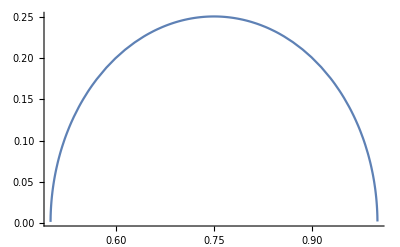

```mathematica
Plot[(√(1/2 (d+l) x-x^2+1/4 (-d l+4 ϵ^2)))//.{d->1 ,l-> 2,ϵ-> 1/100},{x,0.4,1.1},PlotRange->All]
```

```mathematica
(*Good!*)
```

```mathematica
{√(b+a x-x^2)//.{x-> -l/2},√(b+a x-x^2)//.{x->-d/2}}
```

{√(b-(a l)/2-l^2/4),√(b-(a d)/2-d^2/4)}

```mathematica
Flatten[Solve[{√(b-(a l)/2-l^2/4)==ϵ,√(b-(a d)/2-d^2/4)==ϵ},{a,b}]]
```

{a→1/2 (-d-l),b→1/4 (-d l+4 ϵ^2)}

```mathematica
z->√(b+a x-x^2)//.{a->1/2 (-d-l),b->1/4 (-d l+4 ϵ^2)}
```

z→√(1/2 (-d-l) x-x^2+1/4 (-d l+4 ϵ^2))

```mathematica
(*Second curve for interval x ∈ [-l/2,-d/2]*)
```

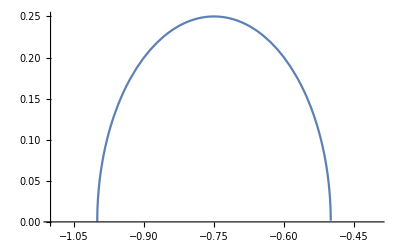

```mathematica
Plot[(√(1/2 (-d-l) x-x^2+1/4 (-d l+4 ϵ^2)))//.{d->1 ,l-> 2,ϵ-> 0},{x,-1.1,-0.4}]
```

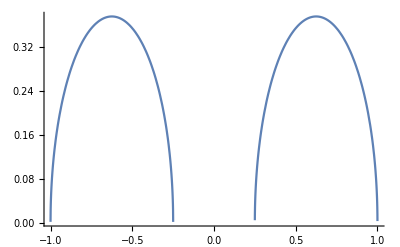

```mathematica
Plot[{(√(1/2 (d+l) x-x^2+1/4 (-d l+4 ϵ^2))),(√(-1/2 (d+l) x-x^2+1/4 (-d l+4 ϵ^2)))}//.{d->1/2,l-> 2,ϵ-> 1/100},{x,-1.2,1.2},PlotRange->All]
```

```mathematica
(*Greeeeat! Now we have the curves that enclose the entangling regions for subsystem partitions with separation=d and size (l-d)/2 each*)
```

```mathematica
{√(b+a x-x^2)//.{x-> -d/2},√(b+a x-x^2)//.{x->d/2}}
```

{√(b-(a d)/2-d^2/4),√(b+(a d)/2-d^2/4)}

```mathematica
Flatten[Solve[{√(b-(a d)/2-d^2/4)==ϵ,√(b+(a d)/2-d^2/4)==ϵ},{a,b}]]
```

{a→0,b→1/4 (d^2+4 ϵ^2)}

```mathematica
z->√(b+a x-x^2)//.{a->0,b->1/4 (d^2+4 ϵ^2)}
```

z→√(-x^2+1/4 (d^2+4 ϵ^2))

```mathematica
(*This is the region x ∈ [-d/2,d/2] that encloses the boundary of subsystem partitons, and has a length=d.*)
```

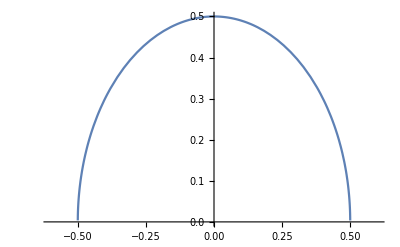

```mathematica
Plot[(√(-x^2+1/4 (d^2+4 ϵ^2)))//.{d->1 ,ϵ-> 0},{x,-0.6,0.6}]
```

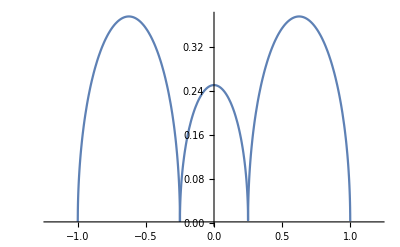

```mathematica
Plot[{(√(1/2 (d+l) x-x^2+1/4 (-d l+4 ϵ^2))),(√(-1/2 (d+l) x-x^2+1/4 (-d l+4 ϵ^2))),(√(-x^2+1/4 (d^2+4 ϵ^2)))}//.{d->1/2,l-> 2,ϵ-> 1/100},{x,-1.2,1.2},PlotRange->Full]
```

```mathematica
(√(1/2 (d+l) x-x^2+1/4 (-d l+4 ϵ^2)))//.{x-> d/2}//FullSimplify
(√(1/2 (d+l) x-x^2+1/4 (-d l+4 ϵ^2)))//.{x->l/2 }//FullSimplify
```

ϵ

ϵ

```mathematica
(√(-1/2 (d+l) x-x^2+1/4 (-d l+4 ϵ^2)))//.{x-> -d/2}//FullSimplify
(√(-1/2 (d+l) x-x^2+1/4 (-d l+4 ϵ^2)))//.{x->-l/2 }//FullSimplify
```

ϵ

ϵ

```mathematica
(√(-x^2+1/4 (d^2+4 ϵ^2)))//.{x-> d/2}//FullSimplify
(√(-x^2+1/4 (d^2+4 ϵ^2)))//.{x-> -d/2}//FullSimplify
```

ϵ

ϵ

#### 2) d=0

```mathematica
{√(b+a x-x^2)//.{x-> -l/2},√(b+a x-x^2)//.{x->+l/2}}
```

{√(b-(a l)/2-l^2/4),√(b+(a l)/2-l^2/4)}

```mathematica
Flatten[Solve[{√(b-(a l)/2-l^2/4)==ϵ,√(b+(a l)/2-l^2/4)==ϵ},{a,b}]]
```

{a→0,b→1/4 (l^2+4 ϵ^2)}

```mathematica
z->√(b+a x-x^2)//.{a->0,b->1/4 (l^2+4 ϵ^2)}
```

z→√(-x^2+1/4 (l^2+4 ϵ^2))

```mathematica
(*Full solution with d=0 for the interval x ∈ [-l/2,l/2]*)
```

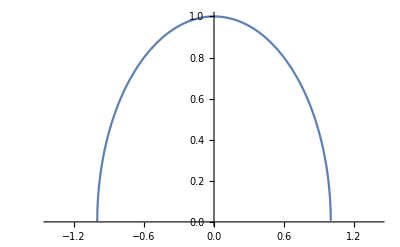

```mathematica
Plot[(√(-x^2+1/4 (l^2+4 ϵ^2)))//.{l-> 2,ϵ-> 0},{x,-1.4,1.4}]
```

```mathematica
(√(-x^2+1/4 (l^2+4 ϵ^2)))//.{x-> l/2}//FullSimplify
(√(-x^2+1/4 (l^2+4 ϵ^2)))//.{x-> -l/2}//FullSimplify
```

ϵ

ϵ

```mathematica
(*Pard0={x-> l/2 Cos[s],z-> l/2 Sin[s]};*)
```

```mathematica
√(l^2+4 ϵ^2)
```

```mathematica
z^2== 1/4 (l^2+4 ϵ^2)-x^2//.{x-> (√(l^2+4 ϵ^2))/2 Cos[s],z-> (√(l^2+4 ϵ^2))/2 Sin[s]}//FullSimplify
```

True

```mathematica
Animate[Plot[{(√(-x^2+1/4 (l^2+4 ϵ^2))),(√(1/2 (d+l) x-x^2+1/4 (-d l+4 ϵ^2))),(√(-1/2 (d+l) x-x^2+1/4 (-d l+4 ϵ^2))),(√(-x^2+1/4 (d^2+4 ϵ^2)))},{x,-5,5},PlotRange->All],{d,0,5},{l,1,5},{ϵ,1/100,1/10},AnimationRunning->False]
```

## Gravitational Action and Complexity = Volume in AdS3 (No need to run)

#### Example for circle in flat spacetime

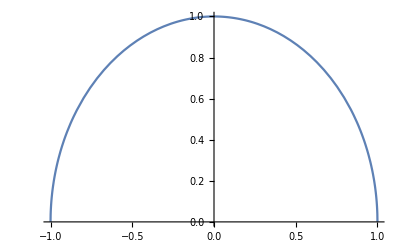

π/2

```mathematica
Plot[√(1-x^2),{x,-1,1}]
Integrate[Integrate[1,{y,0,√(1-x^2)}],{x,-1,1}]
```

#### AdS3 Case

```mathematica
(*{Λ->-1/L^2}*)
```

```mathematica
Table[Einstein[[i,j]]//Simplify,{i,2},{j,2}]
```

{{0,0},{0,0}}

```mathematica
Table[RicciTensor[[i,j]]+1/L^2 metric[[i,j]]//Simplify,{i,2},{j,2}]
```

{{0,0},{0,0}}

```mathematica
RicciScalar//FullSimplify
```

-2/L^2

```mathematica
rg
volumeForm
```

L^2/z^2

(L^2 𝕕[z,x])/z^2

```mathematica
Assuming[{ϵ>0,ϵ<zh},Integrate[Integrate[rg,{z,ϵ,zh}],{x,x1,x2}]]
```

L^2 (-x1+x2) (-1/zh+1/ϵ)

```mathematica
Assuming[{ϵ>0,ϵ<zh},Integrate[rg,{z,ϵ,zh}]]//FullSimplify
```

L^2 (-1/zh+1/ϵ)

```mathematica
(*The normal gravitational action is 0*)
```

```mathematica
(RicciScalar-2(-1/L^2))//Simplify
```

0

```mathematica
Simplify[1/(16 π GN)(rg)*(RicciScalar-2(-1/L^2))]
```

0

```mathematica
Assuming[{ϵ>0,ϵ<zh},Integrate[Integrate[Integrate[-1/(16 π GN)(rg)*(RicciScalar-2(-1/L^2)),{z,ϵ,zh}],{x,x1,x2}],{t,t1,t2}]]//FullSimplify
```

0

## Area enclosed by the RT surface and the ϵ-regulated conformal boundary

```mathematica
Animate[Plot[{(√(-x^2+1/4 (l^2+4 ϵ^2))),(√(1/2 (d+l) x-x^2+1/4 (-d l+4 ϵ^2))),(√(-1/2 (d+l) x-x^2+1/4 (-d l+4 ϵ^2))),(√(-x^2+1/4 (d^2+4 ϵ^2)))},{x,-5,5},PlotRange->All],{d,0,5},{l,1,5},{ϵ,1/100,1/10},AnimationRunning->False]
```

#### Volume enclosed by RT surface for d=0

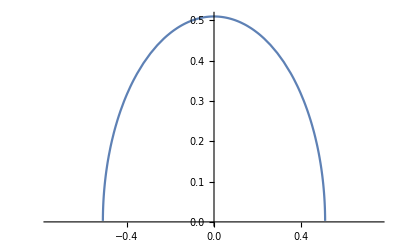

1/4 (-2 l ϵ+(l^2+4 ϵ^2) ArcCot[(2 ϵ)/l])

```mathematica
Plot[(√(-x^2+1/4 (l^2+4 ϵ^2)))//.{l->1 ,ϵ-> 1/10},{x,-3/4,3/4}]
Assuming[l>0,Integrate[Integrate[1,{z,ϵ,√(-x^2+1/4 (l^2+4 ϵ^2))}],{x,-l/2,l/2}]//FullSimplify]
```

```mathematica
(*The previous would be the answer if the spacetime was R2, but it is instead H2*)
```

```mathematica
$Assumptions=And[$Assumptions&& l ∈ Reals && l≥0 && ϵ ∈ Reals && ϵ>0];
```

```mathematica
rg
volumeForm
```

L^2/z^2

(L^2 𝕕[z,x])/z^2

```mathematica
Assuming[l>0,Integrate[Integrate[rg,{z,ϵ,√(-x^2+1/4 (l^2+4 ϵ^2))}],{x,-l/2,l/2}]//FullSimplify]
```

(L^2 (l-2 ϵ ArcCot[(2 ϵ)/l]))/ϵ

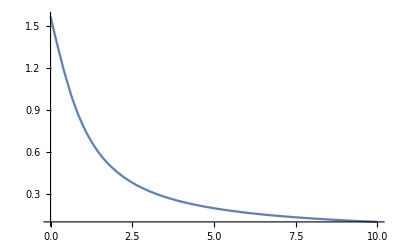

```mathematica
Plot[ArcCot[x],{x,0,10},PlotRange->Full]
```

```mathematica
(L^2 (l-2 ϵ ArcCot[(2 ϵ)/l]))/ϵ//Expand
```

(l L^2)/ϵ-2 L^2 ArcCot[(2 ϵ)/l]

```mathematica
Limit[(L^2 (l-2 ϵ ArcCot[(2 ϵ)/l]))/ϵ,ϵ-> 0]
```

Indeterminate

```mathematica
Limit[(L^2 (l-2 ϵ ArcCot[(2 ϵ)/l]))/ϵ,l-> ∞]
```

∞

```mathematica
Series[((L^2 (l-2 ϵ ArcCot[(2 ϵ)/l]))/ϵ),{l,0,10}]//FullSimplify
```

(L^2 l^3)/(12 ϵ^3)-(L^2 l^5)/(80 ϵ^5)+(L^2 l^7)/(448 ϵ^7)-(L^2 l^9)/(2304 ϵ^9)+O[l]^11

```mathematica
VolΣRTlFull[L_,l_,ϵ_]:=((l L^2)/ϵ-2 L^2 ArcCot[(2 ϵ)/l]);
```

```mathematica
Assuming[d>0,Integrate[Integrate[rg,{z,ϵ,√(-x^2+1/4 (d^2+4 ϵ^2))}],{x,-d/2,d/2}]//FullSimplify]
```

(L^2 (d-2 ϵ ArcCot[(2 ϵ)/d]))/ϵ

```mathematica
VolΣRTdFull[L_,d_,ϵ_]:=((d L^2)/ϵ-2 L^2 ArcCot[(2 ϵ)/d]) ;
```

```mathematica
Assuming[l>d,FullSimplify[(((l L^2)/ϵ-2 L^2 ArcCot[(2 ϵ)/l]))-((d L^2)/ϵ-2 L^2 ArcCot[(2 ϵ)/d]) ]]
```

(L^2 (-d+l+2 ϵ ArcCot[(2 ϵ)/d]-2 ϵ ArcCot[(2 ϵ)/l]))/ϵ

```mathematica
TrigExpand[(L^2 (-d+l+2 ϵ ArcCot[(2 ϵ)/d]-2 ϵ ArcCot[(2 ϵ)/l]))/ϵ]
```

-(d L^2)/ϵ+(l L^2)/ϵ+2 L^2 ArcCot[(2 ϵ)/d]-2 L^2 ArcCot[(2 ϵ)/l]

```mathematica
VolΣRTstrip[L_,l_,d_,ϵ_]:=((l-d) L^2)/ϵ-2 L^2 (ArcCot[(2 ϵ)/l]-ArcCot[(2 ϵ)/d]) ;
```

```mathematica
Limit[VolΣRTstrip[L,l,d_,ϵ],d-> 0]
```

lim_(d→0) (-2 L^2 (ArcCot[(2 ϵ)/l]-ArcCot[(2 ϵ)/d_])+(L^2 (l-d_))/ϵ)

```mathematica
(*Define w as the length of one of the spatial subregions: w=(l-d)/2; Then l=2w+d*)
```

```mathematica
d/w//.{w-> (l-d)/2}//FullSimplify
```

(2 d)/(-d+l)

```mathematica
VolΣRTstrip[L,d+2w,d,ϵ]//FullSimplify
```

(2 L^2 (w+ϵ ArcCot[(2 ϵ)/d]-ϵ ArcCot[(2 ϵ)/(d+2 w)]))/ϵ

```mathematica
D[VolΣRTstrip[L,d+2w,d,ϵ],d]//FullSimplify
```

(16 L^2 w (d+w) ϵ)/((d^2+4 ϵ^2) ((d+2 w)^2+4 ϵ^2))

```mathematica
(*Animate[Plot[VolΣRTstrip[1,d+2w,d,1/10],{d,0,10},PlotRange->All],{w,0,10},AnimationRunning->False]*)
```

```mathematica
(*Animate[Plot[{(√(-x^2+1/4 (l^2+4 ϵ^2))),(√(-x^2+1/4 (d^2+4 ϵ^2)))},{x,-5,5},PlotRange->All],{d,0,5},{l,1,5},{ϵ,1/100,1/10},AnimationRunning->False]*)
```

#### Volume enclosed by RT surface for d≠0

```mathematica
(*Animate[Plot[{(√(1/2 (d+l) x-x^2+1/4 (-d l+4 ϵ^2))),(√(-1/2 (d+l) x-x^2+1/4 (-d l+4 ϵ^2)))},{x,-5,5},PlotRange->All],{d,0,5},{l,1,5},{ϵ,1/100,1/10},AnimationRunning->False]*)
```

```mathematica
Assuming[l>0&&d>0&&l>d,Integrate[Integrate[rg,{z,ϵ,√(1/2 (d+l) x-x^2+1/4 (-d l+4 ϵ^2))}],{x,d/2,l/2}]//FullSimplify]
```

(L^2 (-d+l+4 ϵ ArcCot[(4 ϵ)/(d-l)]))/(2 ϵ)

```mathematica
Assuming[l>0&&d>0&&l>d,Integrate[Integrate[rg,{z,ϵ,√(-1/2 (d+l) x-x^2+1/4 (-d l+4 ϵ^2))}],{x,-l/2,-d/2}]//FullSimplify]
```

(L^2 (-d+l+4 ϵ ArcCot[(4 ϵ)/(d-l)]))/(2 ϵ)

```mathematica
Expand[(L^2 (-d+l+4 ϵ ArcCot[(4 ϵ)/(d-l)]))/(2 ϵ)]
```

-(d L^2)/(2 ϵ)+(l L^2)/(2 ϵ)+2 L^2 ArcCot[(4 ϵ)/(d-l)]

```mathematica
VolΣRTdlPartial[L_,l_,d_,ϵ_]:=((l-d) L^2)/(2 ϵ)-2 L^2 ArcCot[(4 ϵ)/(l-d)] ;
```

```mathematica
VolΣRTdlFull[L_,l_,d_,ϵ_]:=((l-d) L^2)/ϵ-4 L^2 ArcCot[(4 ϵ)/(l-d)];
```

```mathematica
(*Animate[Plot[VolΣRTdlFull[1,d+2w,d,1/10],{d,0,10},PlotRange->All],{w,1,10},AnimationRunning->False]*)
```

```mathematica
VolΣRTdlPartial[L,l,d,ϵ]
VolΣRTdlFull[L,l,d,ϵ]
```

((-d+l) L^2)/(2 ϵ)-2 L^2 ArcCot[(4 ϵ)/(-d+l)]

((-d+l) L^2)/ϵ-4 L^2 ArcCot[(4 ϵ)/(-d+l)]

```mathematica
VolΣRTlFull[L,l,ϵ]
VolΣRTdFull[L,d,ϵ]
VolΣRTstrip[L,l,d,ϵ]
```

(l L^2)/ϵ-2 L^2 ArcCot[(2 ϵ)/l]

(d L^2)/ϵ-2 L^2 ArcCot[(2 ϵ)/d]

((-d+l) L^2)/ϵ-2 L^2 (-ArcCot[(2 ϵ)/d]+ArcCot[(2 ϵ)/l])

#### Quick d=0 Analysis

```mathematica
Limit[VolΣRTdlPartial[L,l,d,ϵ],d-> 0]//FullSimplify
Limit[VolΣRTdlFull[L,l,d,ϵ],d-> 0]//FullSimplify
```

(L^2 (l-4 ϵ ArcCot[(4 ϵ)/l]))/(2 ϵ)

(L^2 (l-4 ϵ ArcCot[(4 ϵ)/l]))/ϵ

```mathematica
Limit[VolΣRTlFull[L,l,ϵ],d-> 0]//FullSimplify
Limit[VolΣRTdFull[L,d,ϵ],d-> 0]//FullSimplify
Limit[VolΣRTstrip[L,l,d,ϵ],d-> 0]//FullSimplify
```

(L^2 (l-2 ϵ ArcCot[(2 ϵ)/l]))/ϵ

0

(L^2 (l-2 ϵ ArcCot[(2 ϵ)/l]))/ϵ

```mathematica
(*Good!*)
```

#### Back to Business

```mathematica
VolΣRTstrip[L,l,d,ϵ]-VolΣRTdlFull[L,l,d,ϵ]//FullSimplify
```

2 L^2 (ArcCot[(2 ϵ)/d]-ArcCot[(2 ϵ)/l]+2 ArcCot[(4 ϵ)/(-d+l)])

```mathematica
2 L^2 (ArcCot[(2 ϵ)/d]-ArcCot[(2 ϵ)/l]+2 ArcCot[(4 ϵ)/(-d+l)])//.{L-> 1,l-> 2,d-> 1,ϵ-> 1/1000000000}//N
```

6.28319

```mathematica
(*w=(l-d)/2;*)
```

```mathematica
Solve[w== (l-d)/2,l]
```

{{l→d+2 w}}

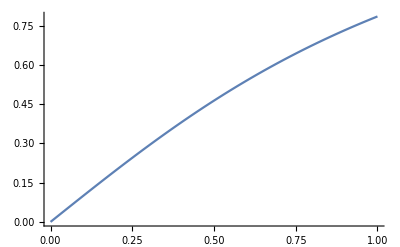

```mathematica
Plot[ArcCot[1/x],{x,0,1},PlotRange->All]
```

```mathematica
ΔVolΣRTStrldFull[L_,l_,d_,ϵ_]:=2 L^2 (ArcCot[(2 ϵ)/d]-ArcCot[(2 ϵ)/l]+2 ArcCot[(4 ϵ)/(l-d)]);
```

```mathematica
Limit[ΔVolΣRTStrldFull[L,l,d,ϵ],d-> 0]//FullSimplify
```

-2 L^2 (ArcCot[(2 ϵ)/l]-2 ArcCot[(4 ϵ)/l])

```mathematica
ΔVolΣRTStrldFull[L,d+2 w,d,ϵ]//FullSimplify
```

2 L^2 (ArcCot[(2 ϵ)/d]-2 ArcCot[(2 ϵ)/w]-ArcCot[(2 ϵ)/(d+2 w)])

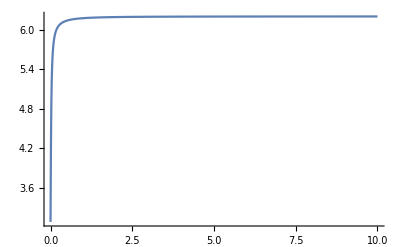

```mathematica
Plot[ΔVolΣRTStrldFull[1,d+2 ,d,1/100],{d,0,10},PlotRange->All]
```

```mathematica
(*Animate[Plot[{ΔVolΣRTStrldFull[1,d+2 w,d,1/10],VolΣRTstrip[1,d+2w,d,1/10]},{d,0,10},PlotRange->All],{w,1,10},AnimationRunning->False]*)
```

## Holographic Subregion Complexity - Volume Proposal

## Summary of Functions in the Poincaré Patch (z, t=const. , x)

Here we compute holographic complexity of subregions for the volume proposal. Our spatial subregion at the conformal boundary consists of two partitions separated by a distance d, each one of lenght (l-d)/2. Then we consider the volume enclosed by the RT surface and the boundary and compute the Volume (Area in this case) of this region. This should correspond to the complexity of the mixed state living in the boundary spatial subregion corresponding to a mixed substate of the CFT vacuum.

Important: As mentioned in the previous sections, these calculations only make sense for small ϵ.

As a simplification, we make the two subregions A1 and B1 of the same size.

```mathematica
$Assumptions=And[$Assumptions&& L ∈ Reals && l ∈ Reals && d ∈ Reals && ϵ ∈ Reals && l≥ d && d≥ 0 && l≥ 0 && ϵ≥0 && w∈ Reals && w ≥ 0];
```

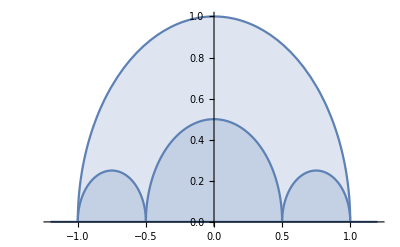

```mathematica
Plot[{(√(-x^2+1/4 (l^2+4 ϵ^2))),(√(1/2 (d+l) x-x^2+1/4 (-d l+4 ϵ^2))),(√(-1/2 (d+l) x-x^2+1/4 (-d l+4 ϵ^2))),(√(-x^2+1/4 (d^2+4 ϵ^2))),ϵ}//.{d-> 1,l-> 2,ϵ-> 1/10000},{x,-1.2,1.2},PlotRange->All,Filling->Axis]
```

Uncomment the following for an animated graph of the previous plot.

```mathematica
(*Animate[Plot[{(√(-x^2+1/4 (l^2+4 ϵ^2))),(√(1/2 (d+l) x-x^2+1/4 (-d l+4 ϵ^2))),(√(-1/2 (d+l) x-x^2+1/4 (-d l+4 ϵ^2))),(√(-x^2+1/4 (d^2+4 ϵ^2)))},{x,-5,5},PlotRange->All],{d,0,5},{l,1,5},{ϵ,1/100,1/10},AnimationRunning->False]*)
```

L= AdS3 radius;
ϵ= Regulator/Bulk Cutoff. We need to assume it to be very small for the calculations to actually make sense;
d= Separation between the subregion partitions at the cutoff surface z=ϵ;
w=Length of each of the subregion partitions at the cutoff surface z=ϵ;
l= 2w+d ; Total separation between the endpoints of the subregion partitions at the cutoff surface z=ϵ;

```mathematica
VolΣRTdlPartial[L_,l_,d_,ϵ_]:=((-d+l) L^2)/(2 ϵ)-2 L^2 ArcCot[(4 ϵ)/(-d+l)];
VolΣRTdlFull[L_,l_,d_,ϵ_]:=((-d+l) L^2)/ϵ-4 L^2 ArcCot[(4 ϵ)/(-d+l)];
VolΣRTlFull[L_,l_,ϵ_] :=(l L^2)/ϵ-2 L^2 ArcCot[(2 ϵ)/l];
VolΣRTdFull[L_,d_,ϵ_]:=(d L^2)/ϵ-2 L^2 ArcCot[(2 ϵ)/d];
VolΣRTstrip[L_,l_,d_,ϵ_]:=((-d+l) L^2)/ϵ-2 L^2 (-ArcCot[(2 ϵ)/d]+ArcCot[(2 ϵ)/l]);
ΔVolΣRTStrldFull[L_,l_,d_,ϵ_]:=2 L^2 (ArcCot[(2 ϵ)/d]-ArcCot[(2 ϵ)/l]+2 ArcCot[(4 ϵ)/(-d+l)]);
```

```mathematica
VolΣRTdlPartial[L,l,d,ϵ] (*This is the Volume (Area in this case) enclosed by the RT surface and the spatial subregions x ∈ [d/2,l/2], and x ∈ [-l/2,-d/2] - This corresponds to Cv(ρA1)=Cv(ρB1)*)
VolΣRTdlFull[L,l,d,ϵ] (* VolΣRTdlFull[L,l,d,ϵ] = 2 VolΣRTdlPartial[L,l,d,ϵ]. ;This is the total Volume (Area in this case) of the previous surfaces - This corresponds to Cv(ρA1)+Cv(ρB1)*)
```

((-d+l) L^2)/(2 ϵ)-2 L^2 ArcCot[(4 ϵ)/(-d+l)]

((-d+l) L^2)/ϵ-4 L^2 ArcCot[(4 ϵ)/(-d+l)]

```mathematica
VolΣRTlFull[L,l,ϵ] (*This is the Volume (Area in this case) enclosed by the RT surface and the spatial subregion x ∈ [-l/2,l/2]- This corresponds to Cv(ρ(A1UB1)) for d=0*)
VolΣRTdFull[L,d,ϵ](*This is the Volume (Area in this case) enclosed by the RT surface and the spatial subregion x ∈ [-d/2,d/2]- This is the part that we need to subtract from Cv(ρ(A1UB1)) to obtain a formula valid for all d*)
VolΣRTstrip[L,l,d,ϵ](*This is the Volume (Area in this case) of the strip enclosed by the RT surfaces and the spatial subregions x ∈ [-l/2,-d/2]U[d/2,l/2]- This corresponds to Cv(ρ(A1UB1)) for all d*)
```

(l L^2)/ϵ-2 L^2 ArcCot[(2 ϵ)/l]

(d L^2)/ϵ-2 L^2 ArcCot[(2 ϵ)/d]

((-d+l) L^2)/ϵ-2 L^2 (-ArcCot[(2 ϵ)/d]+ArcCot[(2 ϵ)/l])

```mathematica
ΔVolΣRTStrldFull[L,l,d,ϵ] (* The 'mutual complexity' is the difference between the strip volume and the two small subregion volumes: ΔVolΣRTStrldFull[L,l,d,ϵ] := VolΣRTstrip[L,l,d,ϵ] - VolΣRTdlFull[L,l,d,ϵ] - This corresponds to ΔCv(ρA1UB1) := Cv(ρA1UB1)-(Cv(ρA1)+Cv(ρB1)) *)
```

2 L^2 (ArcCot[(2 ϵ)/d]-ArcCot[(2 ϵ)/l]+2 ArcCot[(4 ϵ)/(-d+l)])

Some people define mutual complexity with the opposite sign. So bear this in mind dear reader.

## Plots and Calculations

```mathematica
ΔVolΣRTStrldFull[L,l,d,0] (*This "mutual complexity" is always constant and finite for ϵ->0.*)
```

2 L^2 π

```mathematica
Limit[VolΣRTlFull[L,l,ϵ] ,l-> 0]
Limit[VolΣRTdFull[L,d,ϵ],d-> 0]
Limit[VolΣRTstrip[L,l,d,ϵ],d-> 0]-VolΣRTlFull[L,l,ϵ]//FullSimplify
```

0

0

0

```mathematica
Limit[VolΣRTlFull[L,l,ϵ] ,ϵ-> 0]
Limit[VolΣRTdFull[L,d,ϵ],ϵ-> 0]
Limit[VolΣRTstrip[L,l,d,ϵ],ϵ-> 0]//FullSimplify
```

Indeterminate

Indeterminate

Indeterminate

```mathematica
Animate[Plot[{VolΣRTlFull[1,d+2w,1/1000],VolΣRTdFull[1,d,1/1000],VolΣRTstrip[1,d+2w,d,1/1000],ΔVolΣRTStrldFull[1,d+2w,d,1/1000]},{d,0,2},PlotRange->All,PlotLegends->{"Vlregion","Vdregion","VStrip","ΔV"}],{w,1,2},AnimationRunning->False]
```

```mathematica
Animate[Plot[{VolΣRTlFull[1,d+2w,1/10],VolΣRTdFull[1,d,1/10],VolΣRTstrip[1,d+2w,d,1/10],ΔVolΣRTStrldFull[1,d+2w,d,1/10]},{d,0,2},PlotRange->All,PlotLegends->{"Vlregion","Vdregion","VStrip","ΔV"}],{w,1,2},AnimationRunning->False]
```

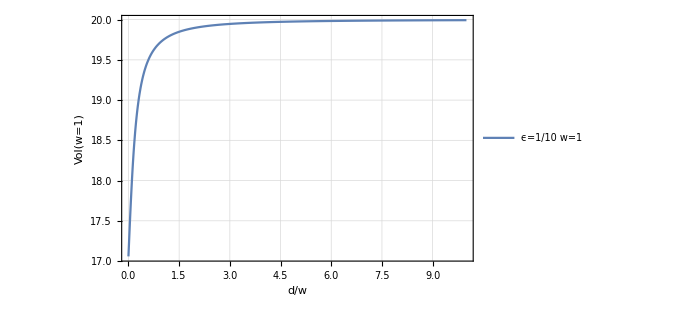

```mathematica
Plot[VolΣRTstrip[1,d+2(1),d,1/10],{d,0,10},PlotTheme->"Detailed",PlotRange->All ,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "Vol(w=1)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"ϵ=1/10 w=1"}]
```

```mathematica
(*Animate[Plot[{ΔVolΣRTStrldFull[1,d+2 w,d,1/10],VolΣRTstrip[1,d+2w,d,1/10]},{d,0,10},PlotRange->All],{w,1,10},AnimationRunning->False]*)
```

```mathematica
ExampleListw1 =Table[Table[{d/w,ΔVolΣRTStrldFull[1,d+2 w,d,1/10000]//N},{d,0,10,1}],{w,1,10}]
```

{{{0,2.55135},{1,5.23195},{2,5.39418},{3,5.44042},{4,5.46033},{5,5.47077},{6,5.47695},{7,5.48091},{8,5.48361},{9,5.48553},{10,5.48694}},{{0,2.84283},{1/2,5.56968},{1,5.75182},{3/2,5.8085},{2,5.83458},{5/2,5.84899},{3,5.85786},{7/2,5.86374},{4,5.86785},{9/2,5.87084},{5,5.87309}},{{0,2.94196},{1/3,5.67925},{2/3,5.86756},{1,5.92821},{4/3,5.95699},{5/3,5.97331},{2,5.9836},{7/3,5.99055},{8/3,5.99549},{3,5.99914},{10/3,6.00192}},{{0,2.99175},{1/4,5.733},{1/2,5.92401},{3/4,5.98658},{1,6.01677},{5/4,6.03416},{3/2,6.04528},{7/4,6.05289},{2,6.05836},{9/4,6.06244},{5/2,6.06558}},{{0,3.02167},{1/5,5.76484},{2/5,5.95726},{3/5,6.0209},{4/5,6.05192},{1,6.06998},{6/5,6.08163},{7/5,6.08967},{8/5,6.0955},{9/5,6.09989},{2,6.10328}},{{0,3.04164},{1/6,5.78588},{1/3,5.97913},{1/2,6.04343},{2/3,6.07498},{5/6,6.09347},{1,6.10548},{7/6,6.11383},{4/3,6.11991},{3/2,6.12451},{5/3,6.12809}},{{0,3.05591},{1/7,5.8008},{2/7,5.99459},{3/7,6.05932},{4/7,6.09124},{5/7,6.11003},{6/7,6.12229},{1,6.13085},{8/7,6.13712},{9/7,6.14188},{10/7,6.1456}},{{0,3.06661},{1/8,5.81194},{1/4,6.00609},{3/8,6.07112},{1/2,6.10329},{5/8,6.1223},{3/4,6.13475},{7/8,6.14347},{1,6.14988},{9/8,6.15477},{5/4,6.1586}},{{0,3.07494},{1/9,5.82057},{2/9,6.01497},{1/3,6.08022},{4/9,6.11258},{5/9,6.13174},{2/3,6.14434},{7/9,6.15318},{8/9,6.15971},{1,6.16469},{10/9,6.1686}},{{0,3.0816},{1/10,5.82745},{1/5,6.02204},{3/10,6.08745},{2/5,6.11995},{1/2,6.13924},{3/5,6.15194},{7/10,6.16088},{4/5,6.16749},{9/10,6.17255},{1,6.17653}}}

```mathematica
ExampleListw1⟦1⟧
```

{{0,2.55135},{1,5.23195},{2,5.39418},{3,5.44042},{4,5.46033},{5,5.47077},{6,5.47695},{7,5.48091},{8,5.48361},{9,5.48553},{10,5.48694}}

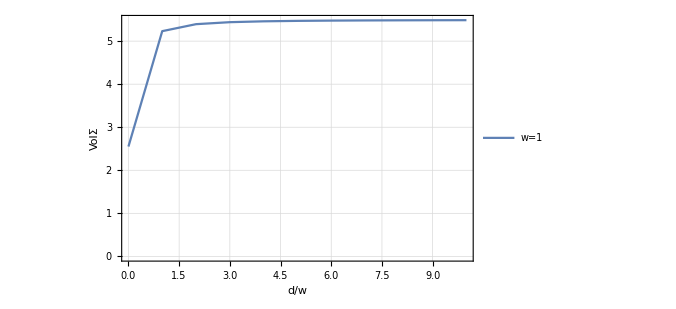

```mathematica
ListPlot[ExampleListw1⟦1⟧,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "VolΣ"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1"}]
```

## Anchoring the RT surfaces at z=0 - Another ϵ-regularisation

### Regulating ϵ

```mathematica
(*Assume z>0*)
```

#### 1) d ≠ 0

```mathematica
{√(b+a x-x^2)//.{x-> l/2},√(b+a x-x^2)//.{x->d/2}}//FullSimplify
```

{√(b+1/4 (2 a-l) l),√(b+1/4 (2 a-d) d)}

```mathematica
(*Anchoring the RT surface to the conformal boundary at z=0:*)
```

```mathematica
Flatten[Solve[{√(b+1/4 (2 a-l) l)==0,√(b+1/4 (2 a-d) d)==0},{a,b}]]
```

{a→(d+l)/2,b→-(d l)/4}

```mathematica
z->√(b+a x-x^2)//.{a->(d+l)/2,b->-(d l)/4}
```

z→√(-(d l)/4+1/2 (d+l) x-x^2)

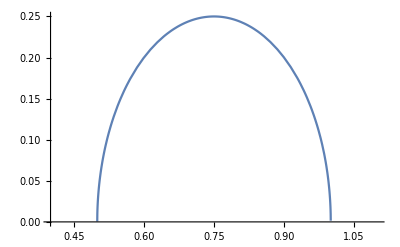

```mathematica
Plot[√(-(d l)/4+1/2 (d+l) x-x^2)//.{d->1 ,l-> 2},{x,0.4,1.1},PlotLegends->"Expressions"]
```

```mathematica
(*Good!*)
```

```mathematica
(*Now for the other part of the geodesic*)
```

```mathematica
Solve[z^2+x^2-a x-b==0,z]
```

{{z→-√(b+a x-x^2)},{z→√(b+a x-x^2)}}

```mathematica
{√(b+a x-x^2)//.{x->-l/2},√(b+a x-x^2)//.{x->-d/2}}//FullSimplify
```

{√(b-1/4 l (2 a+l)),√(b-1/4 d (2 a+d))}

```mathematica
Flatten[Solve[{√(b-1/4 l (2 a+l))==0,√(b-1/4 d (2 a+d))==0},{a,b}]]
```

{a→1/2 (-d-l),b→-(d l)/4}

```mathematica
z->√(b+a x-x^2)//.{a->1/2 (-d-l),b->-(d l)/4}
```

z→√(-(d l)/4+1/2 (-d-l) x-x^2)

```mathematica
Plot[{√(-(d l)/4+1/2 (-d-l) x-x^2)//.{d->1 ,l-> 2}},{x,-1.1,-0.4},PlotLegends->"Expressions"]
```

-Graphics-

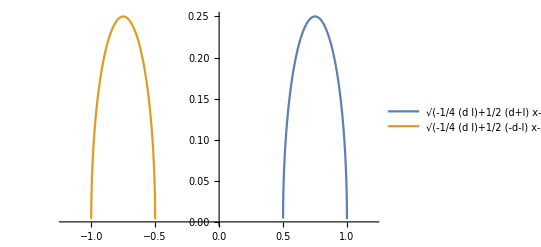

```mathematica
Plot[{√(-(d l)/4+1/2 (d+l) x-x^2)//.{d->1 ,l-> 2},√(-(d l)/4+1/2 (-d-l) x-x^2)//.{d->1 ,l-> 2}},{x,-1.2,1.2},PlotLegends->"Expressions"]
```

```mathematica
(*Greeeeat!*)
```

```mathematica
(*Greeeeat! Now we have the curves that enclose the entangling regions for subsystem partitions with separation=d and size (l-d)/2 each*)
```

```mathematica
{√(b+a x-x^2)//.{x-> -d/2},√(b+a x-x^2)//.{x->d/2}}
```

{√(b-(a d)/2-d^2/4),√(b+(a d)/2-d^2/4)}

```mathematica
Flatten[Solve[{√(b-(a d)/2-d^2/4)==0,√(b+(a d)/2-d^2/4)==0},{a,b}]]
```

{a→0,b→d^2/4}

```mathematica
z->√(b+a x-x^2)//.{a->0,b->d^2/4}
```

z→√(d^2/4-x^2)

```mathematica
(*This is the region x ∈ [-d/2,d/2] that encloses the boundary of subsystem partitons, and has a length=d.*)
```

```mathematica
Plot[{√(d^2/4-x^2)//.d->1 },{x,-0.6,0.6}]
```

-Graphics-

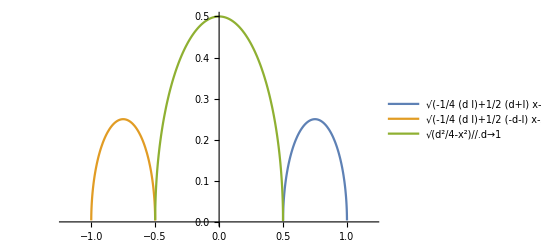

```mathematica
Plot[{√(-(d l)/4+1/2 (d+l) x-x^2)//.{d->1 ,l-> 2},√(-(d l)/4+1/2 (-d-l) x-x^2)//.{d->1 ,l-> 2},√(d^2/4-x^2)//.d->1 },{x,-1.2,1.2},PlotLegends->"Expressions"]
```

#### 2) d = 0:

```mathematica
{√(b+a x-x^2)//.{x-> -l/2},√(b+a x-x^2)//.{x->l/2}}//FullSimplify
```

{√(b-1/4 l (2 a+l)),√(b+1/4 (2 a-l) l)}

```mathematica
Flatten[Solve[{√(b-1/4 l (2 a+l))==0,√(b+1/4 (2 a-l) l)==0},{a,b}]]
```

{a→0,b→l^2/4}

```mathematica
z->√(b+a x-x^2)//.{a->0,b->l^2/4}
```

z→√(l^2/4-x^2)

```mathematica
(*Full solution with d=0*)
```

```mathematica
Plot[√(l^2/4-x^2)//.l-> 2,{x,-1.4,1.4}]
```

-Graphics-

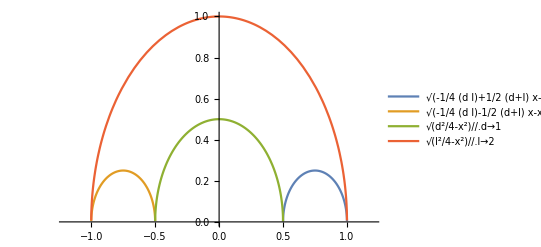

```mathematica
Plot[{√(-(d l)/4+1/2 (d+l) x-x^2)//.{d->1 ,l-> 2},√(-(d l)/4-1/2 (d+l) x-x^2)//.{d->1 ,l-> 2},√(d^2/4-x^2)//.d->1,√(l^2/4-x^2)//.l-> 2 },{x,-1.2,1.2},PlotLegends->"Expressions"]
```

## Calculating the Volumes enclosed by the RT surface and the cutoff surface z=ϵ:

```mathematica
(*Now we need to regulate for z-> 0*)
```

#### Volume enclosed by RT surface for l and d

```mathematica
rg
```

L^2/z^2

```mathematica
(*Big assumption: the x range of integration is actually *)
```

```mathematica
Assuming[l>0&&ϵ>0&&l>ϵ,Integrate[Integrate[rg,{z,ϵ,√(l^2/4-x^2)}],{x,-(l/2-ϵ/2),l/2-ϵ/2}]//FullSimplify]
```

(L^2 (l-ϵ-2 ϵ ArcTan[(l-ϵ)/(√((2 l-ϵ) ϵ))]))/ϵ

```mathematica
Collect[(L^2 (l-ϵ-2 ϵ ArcTan[(l-ϵ)/(√((2 l-ϵ) ϵ))]))/ϵ//Expand,L^2]
```

L^2 (-1+l/ϵ-2 ArcTan[(l-ϵ)/(√((2 l-ϵ) ϵ))])

```mathematica
(l L^2)/ϵ-L^2(1+2 ArcTan[(l-ϵ)/(√((2 l-ϵ) ϵ))])-(L^2 (-1+l/ϵ-2 ArcTan[(l-ϵ)/(√((2 l-ϵ) ϵ))]))//FullSimplify
```

0

```mathematica
(l L^2)/ϵ-L^2(1+2 ArcTan[(l-ϵ)/(√((2 l-ϵ) ϵ))])
```

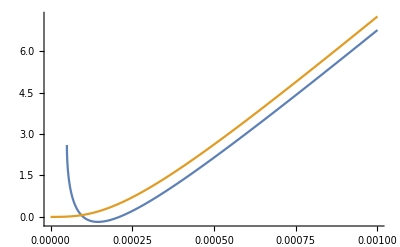

```mathematica
Plot[{(((l L^2)/ϵ-L^2(1+2 ArcTan[(l-ϵ)/(√((2 l-ϵ) ϵ))]))//.{L^2-> 1,ϵ-> 1/10000}),((l L^2)/ϵ -2 L^2 ArcCot[(2 ϵ)/l])//.{L^2-> 1,ϵ-> 1/10000}},{l,0,1/1000},PlotRange->All]
```

```mathematica
{Limit[ArcTan[x],x-> ∞],ArcCot[0]}
```

{π/2,π/2}

```mathematica
{-L^2(1+2 π/2),-2 L^2 π/2}//FullSimplify
```

{-L^2 (1+π),-L^2 π}

```mathematica
VolΣRTlFullV2[L_,l_,ϵ_]:=((l L^2)/ϵ-L^2(1+2 ArcTan[(l-ϵ)/(√((2 l-ϵ) ϵ))]));
```

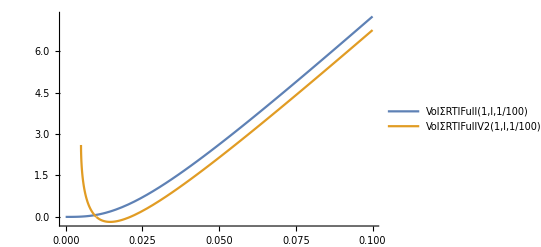

```mathematica
Plot[{VolΣRTlFull[1,l,1/100],VolΣRTlFullV2[1,l,1/100]},{l,0,1/10},PlotLegends->"Expressions",PlotRange->All]
```

```mathematica
Assuming[d>0&&ϵ>0&&d>ϵ,Integrate[Integrate[rg,{z,ϵ,√(d^2/4-x^2)}],{x,-(d/2-ϵ/2),d/2-ϵ/2}]//FullSimplify]
```

(L^2 (d-ϵ-2 ϵ ArcTan[(d-ϵ)/(√((2 d-ϵ) ϵ))]))/ϵ

```mathematica
Collect[Expand[(L^2 (d-ϵ-2 ϵ ArcTan[(d-ϵ)/(√((2 d-ϵ) ϵ))]))/ϵ],L^2]
```

L^2 (-1+d/ϵ-2 ArcTan[(d-ϵ)/(√((2 d-ϵ) ϵ))])

```mathematica
VolΣRTdFullV2[L_,d_,ϵ_]:=((d L^2)/ϵ -L^2(1+2 ArcTan[(d-ϵ)/(√((2 d-ϵ) ϵ))])) ;
```

```mathematica
Assuming[l>d&&d>ϵ,FullSimplify[(VolΣRTlFullV2[L,l,ϵ])-(VolΣRTdFullV2[L,d,ϵ]) ]]
```

(L^2 (-d+l+2 ϵ ArcTan[(d-ϵ)/(√((2 d-ϵ) ϵ))]-2 ϵ ArcTan[(l-ϵ)/(√((2 l-ϵ) ϵ))]))/ϵ

```mathematica
TrigExpand[(L^2 (-d+l+2 ϵ ArcTan[(d-ϵ)/(√((2 d-ϵ) ϵ))]-2 ϵ ArcTan[(l-ϵ)/(√((2 l-ϵ) ϵ))]))/ϵ]
```

-(d L^2)/ϵ+(l L^2)/ϵ+2 L^2 ArcTan[(d-ϵ)/(√((2 d-ϵ) ϵ))]-2 L^2 ArcTan[(l-ϵ)/(√((2 l-ϵ) ϵ))]

```mathematica
VolΣRTstripV2[L_,l_,d_,ϵ_]:=((l-d) L^2)/ϵ-2 L^2 (ArcTan[(l-ϵ)/(√((2 l-ϵ) ϵ))]-ArcTan[(d-ϵ)/(√((2 d-ϵ) ϵ))]) ;
```

```mathematica
VolΣRTstrip[L,l,d,ϵ]-((-d+l) L^2)/ϵ
VolΣRTstripV2[L,l,d,ϵ]-((-d+l) L^2)/ϵ
```

-2 L^2 (-ArcCot[(2 ϵ)/d]+ArcCot[(2 ϵ)/l])

-2 L^2 (-ArcTan[(d-ϵ)/(√((2 d-ϵ) ϵ))]+ArcTan[(l-ϵ)/(√((2 l-ϵ) ϵ))])

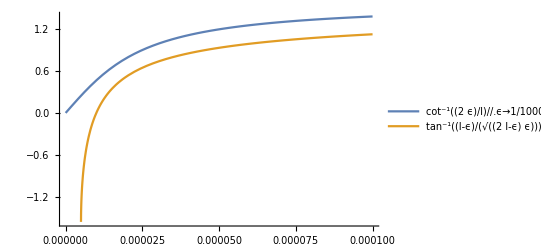

```mathematica
Plot[{ArcCot[(2 ϵ)/l]//.ϵ-> 1/100000,ArcTan[(l-ϵ)/(√((2 l-ϵ) ϵ))]//.ϵ-> 1/100000},{l,0,1/10000},PlotLegends->"Expressions",PlotRange->All]
```

```mathematica
ArcCot[0]
Limit[ArcTan[x],x-> ∞]
```

π/2

π/2

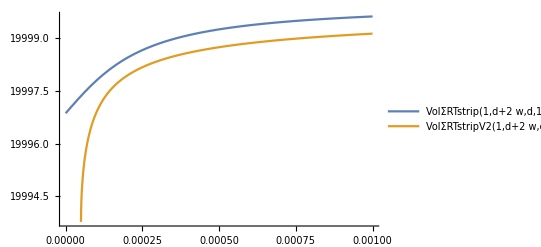

```mathematica
Plot[{VolΣRTstrip[1,d+2w,d,1/10000]//.w-> 1,VolΣRTstripV2[1,d+2w,d,1/10000]//.w-> 1},{d,0,1/1000}//Evaluate,PlotLegends->"Expressions",PlotRange->All]
```

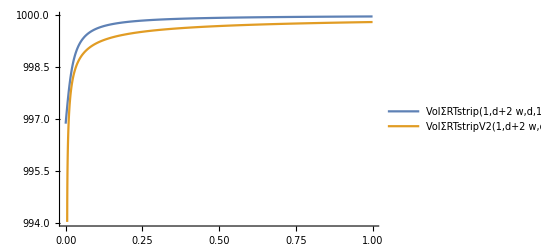

```mathematica
Plot[{VolΣRTstrip[1,d+2w,d,1/100]//.w-> 5,VolΣRTstripV2[1,d+2w,d,1/100]//.w-> 5},{d,0,1}//Evaluate,PlotLegends->"Expressions",PlotRange->All]
```

```mathematica
(*For finite ϵ they behave slightly differently*)
```

```mathematica
Limit[VolΣRTstrip[L,l,d,ϵ],d-> 0]- VolΣRTlFull[L,l,ϵ]//FullSimplify
Limit[VolΣRTstripV2[L,l,d,ϵ],d-> 0]- VolΣRTlFullV2[L,l,ϵ]//FullSimplify
```

0

L^2 (1+(ϵ (-∞))/(√(-Sign[ϵ]^2)))

```mathematica
(*Second one should be zero*)
```

```mathematica
(*Define w as the length of one of the spatial subregions: w=(l-d)/2; Then l=2w+d*)
```

```mathematica
VolΣRTstripV2[L,d+2w,d,ϵ]//FullSimplify
```

(2 L^2 (w+ϵ ArcTan[(d-ϵ)/(√((2 d-ϵ) ϵ))]-ϵ ArcTan[(d+2 w-ϵ)/(√((2 d+4 w-ϵ) ϵ))]))/ϵ

#### Volume enclosed by RT surface for d≠0

```mathematica
Assuming[l>0&&d>0&&l>d&&d>ϵ&&ϵ>0,Integrate[Integrate[rg,{z,ϵ,√(-(d l)/4+1/2 (d+l) x-x^2)}],{x,d/2+ϵ/2,l/2-ϵ/2}]//FullSimplify]
```

∫_((d+ϵ)/2)^((l-ϵ)/2) ConditionalExpression[L^2 (-2/(√((d-2 x) (-l+2 x)))+1/ϵ),(d≠2 x||l<2 x)&&(d>2 x||l≠2 x||d l+4 (x^2+ϵ^2)≤2 (d+l) x)&&(1+2 ϵ Re[1/(√((d-2 x) (-l+2 x))-2 ϵ)]<0||2 ϵ≤Re[√((d-2 x) (-l+2 x))]||√((d-2 x) (-l+2 x))∉ℝ)]ⅆx

```mathematica
Integrate[rg,{z,ϵ,√(-(d l)/4+1/2 (d+l) x-x^2)}]//FullSimplify
```

ConditionalExpression[L^2 (-2/(√((d-2 x) (-l+2 x)))+1/ϵ),(ϵ/(√((d-2 x) (-l+2 x))-2 ϵ)≠0&&Re[ϵ/(√((d-2 x) (-l+2 x))-2 ϵ)]≥0)||Re[ϵ/(√((d-2 x) (-l+2 x))-2 ϵ)]<-1/2||ϵ/(√((d-2 x) (-l+2 x))-2 ϵ)∉ℝ]

```mathematica
Integrate[L^2 (-2/(√((d-2 x) (-l+2 x)))+1/ϵ),{x,d/2+ϵ/2,l/2-ϵ/2}]
```

ConditionalExpression[-(L^2 (d-l+2 ϵ+(4 √(-d+l) ϵ (√-ϵ √((d-l+ϵ)/(d-l)) ArcSinh[(√-ϵ)/(√(-d+l))]-√(-ϵ/(d-l)) √(d-l+ϵ) ArcSinh[(√(d-l+ϵ))/(√(-d+l))]))/(√(-ϵ (d-l+ϵ)))))/(2 ϵ),(Re[(d-l+ϵ)/(d-l+2 ϵ)]>1||Re[(d-l+ϵ)/(d-l+2 ϵ)]<0||(d-l+ϵ)/(d-l+2 ϵ)∉ℝ)&&((Re[ϵ/(d-l+2 ϵ)]≤0&&ϵ/(d-l+2 ϵ)≠0)||Re[ϵ/(d-l+2 ϵ)]>1||ϵ/(d-l+2 ϵ)∉ℝ)]

```mathematica
Collect[Expand[-(L^2 (d-l+2 ϵ+(4 √(-d+l) ϵ (√-ϵ √((d-l+ϵ)/(d-l)) ArcSinh[(√-ϵ)/(√(-d+l))]-√(-ϵ/(d-l)) √(d-l+ϵ) ArcSinh[(√(d-l+ϵ))/(√(-d+l))]))/(√(-ϵ (d-l+ϵ)))))/(2 ϵ)],L^2]
```

L^2 (-1-d/(2 ϵ)+l/(2 ϵ)+(2 √(-d+l) √-ϵ √((d-l+ϵ)/(d-l)) √(-ϵ (d-l+ϵ)) ArcSinh[(√-ϵ)/(√(-d+l))])/(ϵ (d-l+ϵ))-(2 √(-d+l) √(-ϵ/(d-l)) √(-ϵ (d-l+ϵ)) ArcSinh[(√(d-l+ϵ))/(√(-d+l))])/(ϵ √(d-l+ϵ)))

```mathematica
2(√(-d+l) √-ϵ √((d-l+ϵ)/(d-l)) √(-ϵ (d-l+ϵ)) ArcSinh[(√-ϵ)/(√(-d+l))])/(ϵ (d-l+ϵ))//FullSimplify
```

(2 √(-d+l) √ϵ √(1+ϵ/(d-l)) ArcSin[(√ϵ)/(√(-d+l))])/(√(-ϵ (d-l+ϵ)))

```mathematica
-(2 √(-d+l) √(-ϵ/(d-l)) √(-ϵ (d-l+ϵ)) ArcSinh[(√(d-l+ϵ))/(√(-d+l))])/(ϵ √(d-l+ϵ))//FullSimplify
```

(2 √(-d+l) √(-ϵ/(d-l)) √(d-l+ϵ) ArcSinh[(√(d-l+ϵ))/(√(-d+l))])/(√(-ϵ (d-l+ϵ)))

```mathematica
((l-d)L^2)/(2ϵ)-L^2(1-2((√(-d+l) √ϵ √(1+ϵ/(d-l)) ArcSin[(√ϵ)/(√(-d+l))])/(√(-ϵ (d-l+ϵ))))-2((√(-d+l) √(-ϵ/(d-l)) √(d-l+ϵ) ArcSinh[(√(d-l+ϵ))/(√(-d+l))])/(√(-ϵ (d-l+ϵ)))))
```

```mathematica
VolΣRTdlPartialV2[L_,l_,d_,ϵ_]:=((l-d)L^2)/(2ϵ)-L^2(1-2((√(-d+l) √ϵ √(1+ϵ/(d-l)) ArcSin[(√ϵ)/(√(-d+l))])/(√(-ϵ (d-l+ϵ))))-2((√(-d+l) √(-ϵ/(d-l)) √(d-l+ϵ) ArcSinh[(√(d-l+ϵ))/(√(-d+l))])/(√(-ϵ (d-l+ϵ))))) ;
```

```mathematica
VolΣRTdlFullV2[L_,l_,d_,ϵ_]:=((l-d)L^2)/ϵ-2 L^2(1-2((√(-d+l) √ϵ √(1+ϵ/(d-l)) ArcSin[(√ϵ)/(√(-d+l))])/(√(-ϵ (d-l+ϵ))))-2((√(-d+l) √(-ϵ/(d-l)) √(d-l+ϵ) ArcSinh[(√(d-l+ϵ))/(√(-d+l))])/(√(-ϵ (d-l+ϵ)))));
```

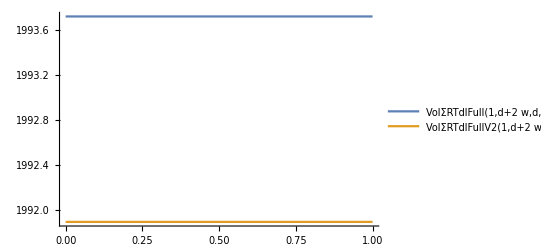

```mathematica
Plot[{VolΣRTdlFull[1,d+2w,d,1/1000]//.{w-> 1},VolΣRTdlFullV2[1,d+2w,d,1/1000]//.{w-> 1}},{d,0,1},PlotLegends->"Expressions",PlotRange->All]
```

```mathematica
VolΣRTdlFullV2[L,l,d,ϵ]-VolΣRTdlFull[L,l,d,ϵ]//FullSimplify
```

2 L^2 (-1+2 ArcCot[(4 ϵ)/(-d+l)]+(2 √(-d+l) √ϵ √(1+ϵ/(d-l)) ArcSin[(√ϵ)/(√(-d+l))])/(√(-ϵ (d-l+ϵ)))+(2 √(-d+l) √(-ϵ/(d-l)) √(d-l+ϵ) ArcSinh[(√(d-l+ϵ))/(√(-d+l))])/(√(-ϵ (d-l+ϵ))))

```mathematica
VolΣRTdlPartialV2[L,l,d,ϵ]
VolΣRTdlFullV2[L,l,d,ϵ]
```

((-d+l) L^2)/(2 ϵ)-L^2 (1-(2 √(-d+l) √ϵ √(1+ϵ/(d-l)) ArcSin[(√ϵ)/(√(-d+l))])/(√(-ϵ (d-l+ϵ)))-(2 √(-d+l) √(-ϵ/(d-l)) √(d-l+ϵ) ArcSinh[(√(d-l+ϵ))/(√(-d+l))])/(√(-ϵ (d-l+ϵ))))

((-d+l) L^2)/ϵ-2 L^2 (1-(2 √(-d+l) √ϵ √(1+ϵ/(d-l)) ArcSin[(√ϵ)/(√(-d+l))])/(√(-ϵ (d-l+ϵ)))-(2 √(-d+l) √(-ϵ/(d-l)) √(d-l+ϵ) ArcSinh[(√(d-l+ϵ))/(√(-d+l))])/(√(-ϵ (d-l+ϵ))))

```mathematica
VolΣRTlFullV2[L,l,ϵ]
VolΣRTdFullV2[L,d,ϵ]
VolΣRTstripV2[L,l,d,ϵ]
```

(l L^2)/ϵ-L^2 (1+2 ArcTan[(l-ϵ)/(√((2 l-ϵ) ϵ))])

(d L^2)/ϵ-L^2 (1+2 ArcTan[(d-ϵ)/(√((2 d-ϵ) ϵ))])

((-d+l) L^2)/ϵ-2 L^2 (-ArcTan[(d-ϵ)/(√((2 d-ϵ) ϵ))]+ArcTan[(l-ϵ)/(√((2 l-ϵ) ϵ))])

```mathematica
VolΣRTstripV2[L,l,d,ϵ]-VolΣRTdlFullV2[L,l,d,ϵ]//FullSimplify
```

(2 L^2 (-2 √(-d+l) √ϵ √(1+ϵ/(d-l)) ArcSin[(√ϵ)/(√(-d+l))]-2 √(-d+l) √(-ϵ/(d-l)) √(d-l+ϵ) ArcSinh[(√(d-l+ϵ))/(√(-d+l))]+√(-ϵ (d-l+ϵ)) (1+ArcTan[(d-ϵ)/(√((2 d-ϵ) ϵ))]-ArcTan[(l-ϵ)/(√((2 l-ϵ) ϵ))])))/(√(-ϵ (d-l+ϵ)))

```mathematica
ΔVolΣRTStrldFullV2[L_,l_,d_,ϵ_]:=(2 L^2 (-2 √(-d+l) √ϵ √(1+ϵ/(d-l)) ArcSin[(√ϵ)/(√(-d+l))]-2 √(-d+l) √(-ϵ/(d-l)) √(d-l+ϵ) ArcSinh[(√(d-l+ϵ))/(√(-d+l))]+√(-ϵ (d-l+ϵ)) (1+ArcTan[(d-ϵ)/(√((2 d-ϵ) ϵ))]-ArcTan[(l-ϵ)/(√((2 l-ϵ) ϵ))])))/(√(-ϵ (d-l+ϵ)));
```

```mathematica
Limit[ΔVolΣRTStrldFullV2[L,d+2w,d,ϵ],d-> 0]//FullSimplify
```

-(2 L^2 (2 √w √ϵ √(2-ϵ/w) ArcSin[(√ϵ)/(√2 √w)]+2 √w √(ϵ/w) √(-2 w+ϵ) ArcSinh[(√(-2 w+ϵ))/(√2 √w)]+√((2 w-ϵ) ϵ) (-1+ArcTan[(2 w-ϵ)/(√((4 w-ϵ) ϵ))]+ArcTan[ϵ/(√(-ϵ^2))])))/(√((2 w-ϵ) ϵ))

```mathematica
ΔVolΣRTStrldFull[L,l,d,0]
```

2 L^2 π

```mathematica
Limit[ΔVolΣRTStrldFullV2[L,l,d,ϵ],ϵ-> 0]
```

Indeterminate

```mathematica
ΔVolΣRTStrldFullV2[1,2,1,1/10]//N
ΔVolΣRTStrldFullV2[1,2,1,1/100]//N
ΔVolΣRTStrldFullV2[1,2,1,1/1000]//N
ΔVolΣRTStrldFullV2[1,2,1,1/100000000000000000]//N
```

5.44225

7.39885

8.00396

8.28319

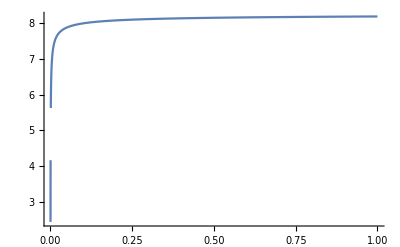

```mathematica
Plot[ΔVolΣRTStrldFullV2[1,d+2(1),d,1/100000000000000]//N,{d,0,1/100000000000},PlotRange->All]
```

## Entanglement Entropy

## Parametrizing the Geodesics

### RT Surface between d/2 and l/2

```mathematica
z^2+x^2-ax+b==0
```

-ax+b+x^2+z^2==0

z→√(-(d l)/4+1/2 (d+l) x-x^2)

```mathematica
z^2==-(d l)/4+1/2 (d+l) x-x^2
```

z^2==-(d l)/4+1/2 (d+l) x-x^2

```mathematica
{x-> r Cos[s]+x0,z-> r Sin[s]}
```

```mathematica
z^2==-(d l)/4+1/2 (d+l) x-x^2//.{x-> r Cos[s]+x0,z-> r Sin[s]}//FullSimplify
```

4 r^2+(d-2 x0) (l-2 x0)==2 r (d+l-4 x0) Cos[s]

```mathematica
Collect[Expand[4 r^2+(d-2 x0) (l-2 x0)-2 r (d+l-4 x0) Cos[s]],r]
```

d l+4 r^2-2 d x0-2 l x0+4 x0^2+r (-2 d Cos[s]-2 l Cos[s]+8 x0 Cos[s])

```mathematica
Solve[{-2 d Cos[s]-2 l Cos[s]+8 x0 Cos[s]==0,d l+4 r^2-2 d x0-2 l x0+4 x0^2==0},{x0,r}]
```

{{x0→(d+l)/4,r→(d-l)/4},{x0→(d+l)/4,r→1/4 (-d+l)}}

```mathematica
z^2==-(d l)/4+1/2 (d+l) x-x^2//.{x-> 1/4 (l-d) Cos[s]+(d+l)/4,z-> 1/4 (l-d) Sin[s]}//FullSimplify
```

True

```mathematica
rg
```

L^2/z^2

```mathematica
volumeForm
```

(L^2 𝕕[z,x])/z^2

```mathematica
D[(1/4 (l-d) Cos[s]+(d+l)/4),s]//FullSimplify
D[(1/4 (l-d) Sin[s]),s]//FullSimplify
```

1/4 (d-l) Sin[s]

1/4 (-d+l) Cos[s]

```mathematica
dx=1/4 (d-l) Sin[s]ds
dz=1/4 (l-d) Cos[s]ds
```

```mathematica
metric
```

{{L^2/z^2,0},{0,L^2/z^2}}

```mathematica
Sqrt[L^2/(1/4 (l-d) Sin[s])^2((1/4 (d-l) Sin[s]Dt[s])^2+(1/4 (l-d) Cos[s]Dt[s])^2)]//FullSimplify
```

Abs[L] √(Csc[s]^2 Dt[s]^2)

```mathematica
Abs[L]Integrate[Csc[s],{s,δ,π-δ}]
```

Abs[L] ∫_δ^(π-δ) Csc[s]ⅆs

```mathematica
Integrate[Csc[s],s]
```

-Log[Cos[s/2]]+Log[Sin[s/2]]

```mathematica
(((-Log[Cos[s/2]]+Log[Sin[s/2]])//.s-> π-δ) -((-Log[Cos[s/2]]+Log[Sin[s/2]])//.(s->δ)))//FullSimplify
```

2 (Log[Cos[δ/2]]-Log[Sin[δ/2]])

```mathematica
Series[Cos[δ/2],{δ,0,3}]
Series[Sin[δ/2],{δ,0,3}]
```

1-δ^2/8+O[δ]^4

δ/2-δ^3/48+O[δ]^4

```mathematica
2 L (Log[1]-Log[δ/2])
```

-2 L Log[δ/2]

```mathematica
2 L Log[2/δ]
```

```mathematica
(*Assume δ =ϵ/r=(4ϵ)/(l-d) *)
```

```mathematica
2 L Log[2/δ]//.δ ->  (4ϵ)/(l-d)
```

2 L Log[(-d+l)/(2 ϵ)]

```mathematica
LengthγRTdlPartial[L_,l_,d_,ϵ_]:=2 L Log[(l-d)/(2 ϵ)];
```

```mathematica
(*Two surfaces*)
```

```mathematica
LengthγRTdlFull[L_,l_,d_,ϵ_]:=4 L Log[(l-d)/(2 ϵ)];
```

### RT Surface between -l/2 and l/2

```mathematica
z^2+x^2-ax+b==0
```

-ax+b+x^2+z^2==0

z→√(l^2/4-x^2)

```mathematica
z^2==l^2/4-x^2
```

z^2==l^2/4-x^2

```mathematica
{x-> r Cos[s]+x0,z-> r Sin[s]}
```

```mathematica
z^2==l^2/4-x^2//.{x-> r Cos[s],z-> r Sin[s]}//FullSimplify
```

l^2==4 r^2

```mathematica
z^2==l^2/4-x^2//.{x-> l/2 Cos[s],z->l/2 Sin[s]}//FullSimplify
```

True

```mathematica
D[l/2 Cos[s],s]//FullSimplify
D[l/2 Sin[s],s]//FullSimplify
```

-1/2 l Sin[s]

1/2 l Cos[s]

```mathematica
dx=-1/2 l Sin[s]ds
dz=1/2 l Cos[s]ds
```

```mathematica
metric
```

{{L^2/z^2,0},{0,L^2/z^2}}

```mathematica
Sqrt[L^2/(l/2 Sin[s])^2((-1/2 l Sin[s]Dt[s])^2+(1/2 l Cos[s]Dt[s])^2)]//FullSimplify
```

Abs[L] √(Csc[s]^2 Dt[s]^2)

```mathematica
Abs[L]Integrate[Csc[s],{s,δ,π-δ}]
```

```mathematica
2 L Log[2/δ]
```

```mathematica
(*Assume δ =ϵ/r=(4ϵ)/(l-d) *)
```

```mathematica
2 L Log[2/δ]//.δ ->  (2ϵ)/l
```

2 L Log[l/ϵ]

```mathematica
LengthγRTlFull[L_,l_,ϵ_]:=2 L Log[l/ϵ];
```

```mathematica
(*By construction: *)
```

```mathematica
LengthγRTdFull[L_,d_,ϵ_]:=2 L Log[d/ϵ];
```

```mathematica
LengthγRTdlFull[L,l,d,ϵ]
LengthγRTlFull[L,l,ϵ]
LengthγRTdFull[L,d,ϵ]
```

4 L Log[(-d+l)/(2 ϵ)]

2 L Log[l/ϵ]

2 L Log[d/ϵ]

```mathematica
LengthγRTdlFull[L,d+2w,d,ϵ]
```

4 L Log[w/ϵ]

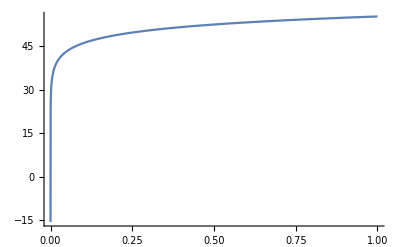

```mathematica
Plot[{LengthγRTdlFull[1,d+2w,d,1/1000000]},{w,0,1},PlotRange->All]
```

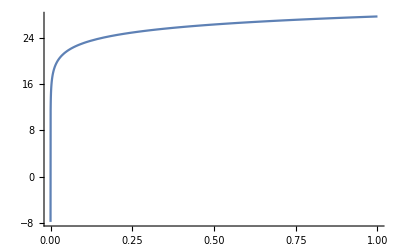

```mathematica
Plot[{LengthγRTlFull[1,l,1/1000000]},{l,0,1},PlotRange->All]
```

```mathematica
Plot[{LengthγRTlFull[1,d,1/1000000]},{d,0,1},PlotRange->All]
```

-Graphics-

```mathematica
LengthγRTdlFull[L,l,d,ϵ]
LengthγRTlFull[L,l,ϵ]
LengthγRTdFull[L,d,ϵ]
```

4 L Log[(-d+l)/(2 ϵ)]

2 L Log[l/ϵ]

2 L Log[d/ϵ]

```mathematica
2 L Log[l/ϵ]+2 L Log[d/ϵ]-4 L Log[(-d+l)/(2 ϵ)]//FullSimplify
```

2 L (Log[(4 d)/ϵ]+Log[l/ϵ]-2 Log[(-d+l)/ϵ])

```mathematica
LengthγRTlFull[L,l,ϵ]+LengthγRTdFull[L,d,ϵ]-LengthγRTdlFull[L,l,d,ϵ]//FullSimplify
```

2 L (Log[(4 d)/ϵ]+Log[l/ϵ]-2 Log[(-d+l)/ϵ])

```mathematica
ΔLengthRTSurfaces[L_,l_,d_,ϵ_]:=2 L (Log[(4 d)/ϵ]+Log[l/ϵ]-2 Log[(l-d)/ϵ]);
```

```mathematica
ΔLengthRTSurfaces[L,d+2w,d,ϵ]//FullSimplify
```

2 L (Log[d/ϵ]-2 Log[w/ϵ]+Log[(d+2 w)/ϵ])

```mathematica
Limit[ΔLengthRTSurfaces[1,l,d,ϵ],d-> 0]
```

-∞

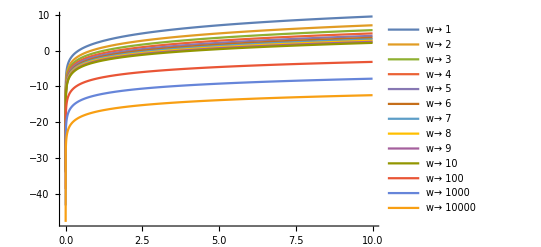

```mathematica
Plot[{ΔLengthRTSurfaces[1,d+2w,d,1/1000000]//.{w-> 1},ΔLengthRTSurfaces[1,d+2w,d,1/1000000]//.{w-> 2},ΔLengthRTSurfaces[1,d+2w,d,1/1000000]//.{w-> 3},ΔLengthRTSurfaces[1,d+2w,d,1/1000000]//.{w-> 4},ΔLengthRTSurfaces[1,d+2w,d,1/1000000]//.{w-> 5},ΔLengthRTSurfaces[1,d+2w,d,1/1000000]//.{w-> 6},ΔLengthRTSurfaces[1,d+2w,d,1/1000000]//.{w-> 7},ΔLengthRTSurfaces[1,d+2w,d,1/1000000]//.{w-> 8},ΔLengthRTSurfaces[1,d+2w,d,1/1000000]//.{w-> 9}
,ΔLengthRTSurfaces[1,d+2w,d,1/1000000]//.{w-> 10},ΔLengthRTSurfaces[1,d+2w,d,1/1000000]//.{w-> 100},ΔLengthRTSurfaces[1,d+2w,d,1/1000000]//.{w-> 1000},ΔLengthRTSurfaces[1,d+2w,d,1/1000000]//.{w-> 10000}},{d,0,10},PlotRange->All,PlotLegends->{"w→ 1","w→ 2","w→ 3","w→ 4","w→ 5","w→ 6","w→ 7","w→ 8","w→ 9","w→ 10","w→ 100","w→ 1000","w→ 10000"}]
```

```mathematica
Plot3D[ΔLengthRTSurfaces[1,l,d,1/1000],{d,0,1},{l,0,1},PlotTheme->"Detailed"]
```

-Graphics3D-

```mathematica
Plot3D[ΔLengthRTSurfaces[1,d+2w,d,ϵ]//.{d-> 1},{w,0,100},{ϵ,1/10,1/100},PlotTheme->"Detailed"]
```

-Graphics3D-